```mathematica
(* 1 Stwórz komendę przyjmującą jako argumenty funkcję,zmienną i granice wykresu i rysującą wykres w kolorach tęczy w okręgach od środka wykresu
*)
```

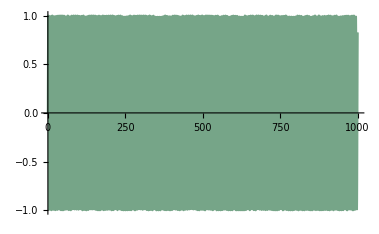

```mathematica
Plot[Sin[x],{x,0,1000}, ColorFunction->Function[{x,y},ColorData["Rainbow"][Sqrt[(x-0.5)^2+(y-0.5)^2]]]]
```

```mathematica
(* 2 Napisz komendę która rysuję wykresy tabeli funkcji w 9 różnych stylach-każdy element inaczej *)
```

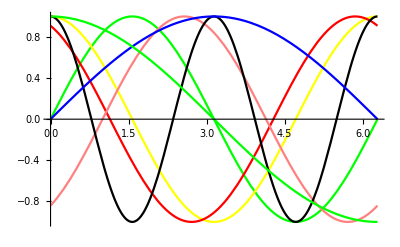

```mathematica
Plot[{Sin[x],Cos[x],Sin[2+x],Sin[x-1],Cos[x*2],Sin[x/2], Cos[0.5*x]},{x,0,2 Pi}, PlotStyle -> {Green, Yellow,Red, Pink, Black, Blue}]
```

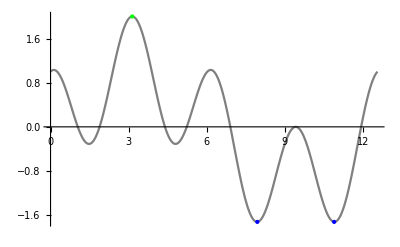

```mathematica
(* 3 Stwórz komendę rysującą wykres funkcji i zaznaczającą zielonymi punktami maksima,a czerwonymi-minima (w danym przedziale) *)
data=Table[{i,Cos[i*2]+Sin[i/2]},{i,0,4 Pi,Pi/100}];ListLinePlot[data, PlotStyle  -> Gray,Epilog->{
PointSize[Large],
Green,Point[MaximalBy[data,N@*Last]],
Blue,Point[MinimalBy[data,N@*Last]]
}
]
```

```mathematica
(* 4 Napisz komendę przyjmującą wykresy funkcji i zwracającą wszystkie wykresy na wspólnym polu.Jeżeli podamy wykresy o dziedzinach {0,1} i {3,5} to wynik będzie wyświetlony w dziedzinie {0,5} itp.(wskazówka:potraktuj wykresy jako listy) *)
```

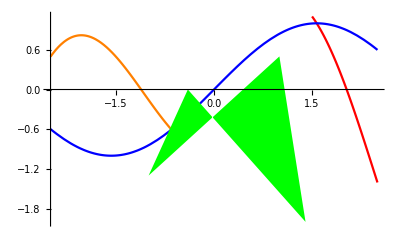

```mathematica
p1=Plot[x Sin[x]-1,{x,-2.5,-0.5}, PlotStyle->Orange];
p2=Plot[Evaluate[D[x Sin[x]-1,x]],{x,1.5,2.5},PlotStyle->Red];
p3=Plot[Sin[x],{x,-2.5,2.5},PlotStyle->Blue];
p4=Graphics[{Green,Polygon[{{1.4,-2},{1,0.5},{-1,-1.3},{-0.4,0}}]}];
lista = {p1, p2, p3, p4};
Show[ lista,PlotRange->All]
```